### Pregunta 1

```mathematica
(*Con el resultado obtenido, metamolo dentro del LHS y veamos que da el RHS*)
```

```mathematica
y1[t_]:= Exp[t]-1
```

```mathematica
Simplify[D[y1[t],{t,2}]+Integrate[Exp[2(t-u)]D[y1[u],{u,1}],{u,0,t}]]
```

ⅇ^(2 t)

```mathematica
(*Si da lo mismo*)
```

### Pregunta 4

```mathematica
InverseZTransform[2-3/z+4/z^2,z,n]
```

4 UnitStep[2-n] UnitStep[-2+n]-3 UnitStep[1-n] UnitStep[-1+n]+2 UnitStep[-n]

```mathematica
(*En lugar de poner un delta, pone 2 heavisides donde el unico punto es igual al del delta ._. *)
```

```mathematica
x4[n_]:=InverseZTransform[2-3/z+4/z^2,z,n]
```

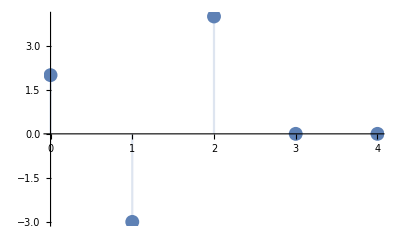

```mathematica
DiscretePlot[x4[n],{n,0,4},PlotStyle->PointSize[0.025]]
```

```mathematica
InverseZTransform[1/(2z)+1/(2 z^2),z,n]
```

1/2 (1-UnitStep[-3+n]) (1-UnitStep[-n])

```mathematica
y4[n_]:=InverseZTransform[1/(2z)+1/(2 z^2),z,n]
```

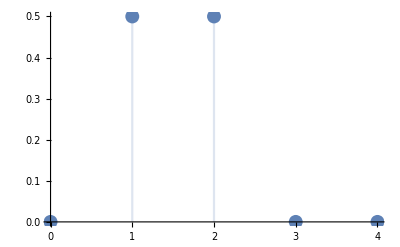

```mathematica
DiscretePlot[y4[n],{n,0,4},PlotStyle->PointSize[0.025]] (*Es nuestro resultado*)
```

```mathematica
Expand[(2-3/z+4/z^2)*(1/(2z)+1/(2 z^2))]
```

2/z^4+1/(2 z^3)-1/(2 z^2)+1/z

```mathematica
(*La convolucion por definicion es*)
```

```mathematica
r4[k_]:=Sum[x4[p]*y4[k-p],{p,0,k}]
```

```mathematica
Table[r4[k],{k,0,11}]
```

{0,1,-1/2,1/2,2,0,0,0,0,0,0,0}

```mathematica
(*Da nuestro resultado*)
```

### Problema 6

#### Parte b

```mathematica
InverseZTransform[(z+2)/(z(z-0.7)),z,k]
```

27. 7.^(-2.+k) 10.^(1.-1. k) (1.-1. UnitStep[1.-1. k])+UnitStep[1.-1. k] UnitStep[-1.+k]

```mathematica
h[k_]:=27. 7.^(-2.+k) 10.^(1.-1. k) (1.-1. UnitStep[1.-1. k])+UnitStep[1.-1. k] UnitStep[-1.+k]
```

```mathematica
Table[h[k],{k,0,9}]
```

{0.,1.,2.7,1.89,1.323,0.9261,0.64827,0.453789,0.317652,0.222357}

```mathematica
Table[-20/7 DiscreteDelta[k-1]-270/49 DiscreteDelta[k]+270/49(0.7)^k,{k,0,9}]
```

{0.,1.,2.7,1.89,1.323,0.9261,0.64827,0.453789,0.317652,0.222357}

```mathematica
(*Vemos que da lo mismo evaluando con la funcion de Transformada inversa que lo obtenido*)
```

#### Parte c

```mathematica
(*Comprobando obteniendo el limite a infinito de la funcion que se obtiene con la Inversa obtenida por Mathematica*)
```

```mathematica
Limit[InverseZTransform[(z+2)/(z(z-0.7))*z/(z-1),z,k],{k->Infinity}]
```

{10.}

```mathematica
Limit[(z-1)(z+2)/(z(z-0.7))*z/(z-1),z->1]
```

10.

```mathematica
(*Dan lo mismo*)
```